```mathematica
SphericalHarmonicY[1,0,θ,ϕ]
```

1/2 √(3/π) Cos[θ]

```mathematica
Integrate[SphericalHarmonicY[1,0,θ,ϕ]^2 Sin[θ], {θ,0,π},{ϕ,0,2π}]
```

1

```mathematica
A[l_]:=((2l+1)/(4π))^(1/2)
```

```mathematica
Integrate[A[1]^2 LegendreP[1,Cos[θ]]^2 Sin[θ], {θ,0,π},{ϕ,0,2π}]
```

1

```mathematica
LegendreP[1,Cos[θ]]
```

Cos[θ]

```mathematica
With[{K=2,P=0},SphericalPlot3D[Re[SphericalHarmonicY[K,P,θ,ϕ]],{θ,0,π},{ϕ,0,2π}]]
```

-Graphics3D-

left hand side Poisson

```mathematica
∑_(l=0)^2 c[n,l]Y[l,0]R2[n,l][r]
```

```mathematica
c[n,0]  D[r R[n,0][r],r,r] Y[0,0]+c[n,1]( D[r R[n,1][r],r,r]-2R[n,1][r]) Y[1,0]+c[n,2] (D[r R[n,2][r],r,r]-6R[n,2][r])Y[2,0]
```

c[n,0] Y[0,0] R2[n,0][r]+c[n,1] Y[1,0] R2[n,1][r]+c[n,2] Y[2,0] R2[n,2][r]+c[n,3] Y[3,0] R2[n,3][r]

```mathematica
R2[n,l][r]= D[r R[n,l][r],r,r]-l(l+1)R[n,l][r]
```

-l (1+l) R[n,l][r]+2 R[n,l]'[r]+r R[n,l]''[r]

right hand side Poisson

```mathematica
∑_(k=0)^2 ∑_(k2=0)^2 ∑_(K=0)^4 Y[K,0]d[s,k]d[s2,k2]J[s,k]J[s2,k2]ClebschGordan[{k,0},{k2,0},{K,0}]ClebschGordan[{k,0},{k2,0},{K,0}] √(((2k+1)(2 k2+1))/(4π(2K+1)))
```

```mathematica
((d[s,0] d[s2,0] J[s,0] J[s2,0])/(2 √π)+(d[s,1] d[s2,1] J[s,1] J[s2,1])/(2 √π)+(d[s,2] d[s2,2] J[s,2] J[s2,2])/(2 √π) )Y[0,0]+((d[s,1] d[s2,0] J[s,1] J[s2,0])/(2 √π)+(d[s,0] d[s2,1] J[s,0] J[s2,1])/(2 √π)+(d[s,2] d[s2,1] J[s,2] J[s2,1])/(√(5 π))+(d[s,1] d[s2,2] J[s,1] J[s2,2])/(√(5 π)))Y[1,0]+((d[s,2] d[s2,0] J[s,2] J[s2,0])/(2 √π)+(d[s,1] d[s2,1] J[s,1] J[s2,1])/(√(5 π))+(d[s,0] d[s2,2] J[s,0] J[s2,2])/(2 √π)+1/7 √(5/π) d[s,2] d[s2,2] J[s,2] J[s2,2]) Y[2,0]+(3/2 √(3/(35 π)) d[s,2] d[s2,1] J[s,2] J[s2,1]+3/2 √(3/(35 π)) d[s,1] d[s2,2] J[s,1] J[s2,2]) Y[3,0]+(3 d[s,2] d[s2,2] J[s,2] J[s2,2] Y[4,0])/(7 √π)
```

las ecs de Poisson

```mathematica
c[n,0]  D[r R[n,0][r],r,r]== (d[s,0] d[s2,0] J[s,0] J[s2,0])/(2 √π)+(d[s,1] d[s2,1] J[s,1] J[s2,1])/(2 √π)+(d[s,2] d[s2,2] J[s,2] J[s2,2])/(2 √π)
```

```mathematica
c[n,1]( D[r R[n,1][r],r,r]-2R[n,1][r]) ==(d[s,1] d[s2,0] J[s,1] J[s2,0])/(2 √π)+(d[s,0] d[s2,1] J[s,0] J[s2,1])/(2 √π)+(d[s,2] d[s2,1] J[s,2] J[s2,1])/(√(5 π))+(d[s,1] d[s2,2] J[s,1] J[s2,2])/(√(5 π))
```

```mathematica
c[n,2] (D[r R[n,2][r],r,r]-6R[n,2][r])==(d[s,2] d[s2,0] J[s,2] J[s2,0])/(2 √π)+(d[s,1] d[s2,1] J[s,1] J[s2,1])/(√(5 π))+(d[s,0] d[s2,2] J[s,0] J[s2,2])/(2 √π)+1/7 √(5/π) d[s,2] d[s2,2] J[s,2] J[s2,2]
```

```mathematica
0==3/2 √(3/(35 π)) d[s,2] d[s2,1] J[s,2] J[s2,1]+3/2 √(3/(35 π)) d[s,1] d[s2,2] J[s,1] J[s2,2]
```

```mathematica
0==(3 d[s,2] d[s2,2] J[s,2] J[s2,2])/(7 √π)
```

left hand side Schrodinger

```mathematica
∑_(s=0)^2 ∑_(k=0)^2 d[s,k]Y[k,0]J2[s,k][r]
```

```mathematica
(d[0,0]  J2[0,0][r]+d[1,0] J2[1,0][r]+d[2,0]  J2[2,0][r]) Y[0,0]+(d[0,1] J2[0,1][r]+d[1,1]  J2[1,1][r]+d[2,1] J2[2,1][r])Y[1,0]+(d[0,2] J2[0,2][r]+d[1,2] J2[1,2][r]+d[2,2] J2[2,2][r]) Y[2,0]
```

```mathematica
(d[0,0]   D[r J[0,0][r],r,r]+d[1,0]  D[r J[1,0][r],r,r]+d[2,0]  D[r J[2,0][r],r,r]) Y[0,0]+(d[0,1] (D[r J[2,1][r],r,r]-2J[2,1][r])+d[1,1] (D[r J[1,1][r],r,r]-2J[1,1][r])+d[2,1](D[r J[2,1][r],r,r]-2J[2,1][r]))Y[1,0]+(d[0,2] (D[r J[0,2][r],r,r]-6J[0,2][r])+d[1,2](D[r J[1,2][r],r,r]-6J[1,2][r])+d[2,2] (D[r J[2,2][r],r,r]-6J[2,2][r])) Y[2,0]
```

```mathematica
J2[s,k][r]= D[r J[s,k][r],r,r]-k(k+1)J[s,k][r]
```

-k (1+k) J[s,k][r]+2 J[s,k]'[r]+r J[s,k]''[r]

right hand side Schrodinger

```mathematica
∑_(l=0)^2 ∑_(k=0)^2 ∑_(L=0)^4 Y[L,0]J[s,k][r] R[n,l][r] c[n,l] d[s,k] ClebschGordan[{k,0},{l,0},{L,0}]ClebschGordan[{k,0},{l,0},{L,0}] √(((2l+1)(2 k+1))/(4π(2L+1)))
```

```mathematica
((c[n,0] d[s,0] J[s,0][r] R[n,0][r])/(2 √π)+(c[n,1] d[s,1]  J[s,1][r] R[n,1][r])/(2 √π)+(c[n,2] d[s,2] J[s,2][r] R[n,2][r])/(2 √π) )Y[0,0]+((c[n,0] d[s,1]  J[s,1][r] R[n,0][r])/(2 √π)+(c[n,1] d[s,2] J[s,2][r] R[n,1][r])/(√(5 π))+(c[n,1] d[s,0]  J[s,0][r] R[n,1][r])/(2 √π)+(c[n,2] d[s,1]  J[s,1][r] R[n,2][r])/(√(5 π)))Y[1,0]+((c[n,0] d[s,2] J[s,2][r] R[n,0][r])/(2 √π)+(c[n,1] d[s,1]  J[s,1][r] R[n,1][r])/(√(5 π))+(c[n,2] d[s,0] J[s,0][r] R[n,2][r])/(2 √π)+1/7 √(5/π) c[n,2] d[s,2]  J[s,2][r] R[n,2][r]) Y[2,0]+(3/2 √(3/(35 π)) c[n,1] d[s,2] J[s,2][r] R[n,1][r]+3/2 √(3/(35 π)) c[n,2] d[s,1] J[s,1][r] R[n,2][r])Y[3,0] +(3 c[n,2] d[s,2] Y[4,0] J[s,2][r] R[n,2][r])/(7 √π)
```

ecs de Schrodinger

```mathematica
d[0,0]   D[r J[0,0][r],r,r]+d[1,0]  D[r J[1,0][r],r,r]+d[2,0]  D[r J[2,0][r],r,r]==∑_(n=0)^2 ∑_(s=0)^2 ((c[n,0] d[s,0] J[s,0][r] R[n,0][r])/(2 √π)+(c[n,1] d[s,1]  J[s,1][r] R[n,1][r])/(2 √π)+(c[n,2] d[s,2] J[s,2][r] R[n,2][r])/(2 √π))
```

```mathematica
d[0,1] (D[r J[2,1][r],r,r]-2J[2,1][r])+d[1,1] (D[r J[1,1][r],r,r]-2J[1,1][r])+d[2,1](D[r J[2,1][r],r,r]-2J[2,1][r])==∑_(n=0)^2 ∑_(s=0)^2 ((c[n,0] d[s,1]  J[s,1][r] R[n,0][r])/(2 √π)+(c[n,1] d[s,2] J[s,2][r] R[n,1][r])/(√(5 π))+(c[n,1] d[s,0]  J[s,0][r] R[n,1][r])/(2 √π)+(c[n,2] d[s,1]  J[s,1][r] R[n,2][r])/(√(5 π)))
```

```mathematica
d[0,2] (D[r J[0,2][r],r,r]-6J[0,2][r])+d[1,2](D[r J[1,2][r],r,r]-6J[1,2][r])+d[2,2] (D[r J[2,2][r],r,r]-6J[2,2][r])==∑_(n=0)^2 ∑_(s=0)^2 ((c[n,0] d[s,2] J[s,2][r] R[n,0][r])/(2 √π)+(c[n,1] d[s,1]  J[s,1][r] R[n,1][r])/(√(5 π))+(c[n,2] d[s,0] J[s,0][r] R[n,2][r])/(2 √π)+1/7 √(5/π) c[n,2] d[s,2]  J[s,2][r] R[n,2][r])
```

```mathematica
∑_(n=0)^2 ∑_(s=0)^2 ( c[n,1] d[s,2] J[s,2][r] R[n,1][r]+ c[n,2] d[s,1] J[s,1][r] R[n,2][r])==0
```

```mathematica
∑_(n=0)^2 ∑_(s=0)^2 c[n,2] d[s,2] J[s,2][r] R[n,2][r]==0
```

Expansion en series de armonicos

```mathematica
∑_(l=0)^10 ∑_(m=-l)^l Integrate[(Cos[θ]+Sin[2θ])Sin[ϕ]SphericalHarmonicY[l,-m,θ,ϕ] Sin[θ],{θ,0,π},{ϕ,0,2π}]SphericalHarmonicY[l,m,θ,ϕ]
```

-1/64 ⅈ ⅇ^(-ⅈ ϕ) (64+15 π) Cos[θ] Sin[θ]+1/64 ⅈ ⅇ^(ⅈ ϕ) (64+15 π) Cos[θ] Sin[θ]-(45 ⅈ ⅇ^(-ⅈ ϕ) π Cos[θ] (-3+7 Cos[θ]^2) Sin[θ])/1024+(45 ⅈ ⅇ^(ⅈ ϕ) π Cos[θ] (-3+7 Cos[θ]^2) Sin[θ])/1024-(1365 ⅈ ⅇ^(-ⅈ ϕ) π Cos[θ] (5-30 Cos[θ]^2+33 Cos[θ]^4) Sin[θ])/65536+(1365 ⅈ ⅇ^(ⅈ ϕ) π Cos[θ] (5-30 Cos[θ]^2+33 Cos[θ]^4) Sin[θ])/65536-(5355 ⅈ ⅇ^(-ⅈ ϕ) π Cos[θ] (-35+385 Cos[θ]^2-1001 Cos[θ]^4+715 Cos[θ]^6) Sin[θ])/2097152+(5355 ⅈ ⅇ^(ⅈ ϕ) π Cos[θ] (-35+385 Cos[θ]^2-1001 Cos[θ]^4+715 Cos[θ]^6) Sin[θ])/2097152-(169785 ⅈ ⅇ^(-ⅈ ϕ) π Cos[θ] (63-1092 Cos[θ]^2+4914 Cos[θ]^4-7956 Cos[θ]^6+4199 Cos[θ]^8) Sin[θ])/134217728+(169785 ⅈ ⅇ^(ⅈ ϕ) π Cos[θ] (63-1092 Cos[θ]^2+4914 Cos[θ]^4-7956 Cos[θ]^6+4199 Cos[θ]^8) Sin[θ])/134217728

```mathematica
f[θ_,ϕ_]:=%8
```

```mathematica
Plot3D[{-(Cos[θ]+Sin[2θ])Sin[ϕ],f[θ,ϕ]},{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
∑_(l=0)^3 Integrate[(Cos[θ]+Sin[2θ])SphericalHarmonicY[l,0,θ,ϕ] Sin[θ],{θ,0,π},{ϕ,0,2π}]SphericalHarmonicY[l,0,θ,ϕ]
```

1/8 (8+3 π) Cos[θ]-7/64 π (-3 Cos[θ]+5 Cos[θ]^3)

```mathematica
f[θ_]:=%52
```

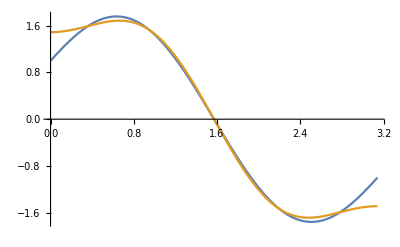

```mathematica
Plot[{(Cos[θ]+Sin[2θ]),f[θ]},{θ,0,π}]
```

```mathematica
l2=2;
m2= 0;
```

```mathematica
∑_(l=0)^l2 ∑_(m=-l)^l ∑_(L=l2-l)^(l+l2) ∑_(M=-L)^L ∑_L2^□ ∑_(M2=-L2)^L2 Y[L2,M2]f[l][r](-1)^m √(((2l+1)(2 l2+1))/(4π(2L+1)))√(((2l+1)(2 l2+1))/(4π(2L2+1)))ClebschGordan[{l,m},{l2,m2},{L,M}]ClebschGordan[{l,0},{l2,0},{L,0}]ClebschGordan[{l,-m},{l2,m2},{L2,M2}]ClebschGordan[{l,0},{l2,0},{L2,0}]KroneckerDelta[l2,L]KroneckerDelta[m2,M]+∑_(l=l2+1)^∞ ∑_(m=-l)^l ∑_(L=l-l2)^(l+l2) ∑_(M=-L)^L ∑_L2^□ ∑_(M2=-L2)^L2 Y[L2,M2]f[l][r](-1)^m √(((2l+1)(2 l2+1))/(4π(2L+1)))√(((2l+1)(2 l2+1))/(4π(2L2+1)))ClebschGordan[{l,m},{l2,m2},{L,M}]ClebschGordan[{l,0},{l2,0},{L,0}]ClebschGordan[{l,-m},{l2,m2},{L2,M2}]ClebschGordan[{l,0},{l2,0},{L2,0}]KroneckerDelta[l2,L]KroneckerDelta[m2,M]
```

ClebschGordan::phy: ThreeJSymbol[{0,0},{2,0},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,0},{2,0},{2,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,0},{2,0},{2,-1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

$Aborted

```mathematica
l2=1;
m2= 0;
```

```mathematica
∑_(l=0)^l2 ∑_(m=-l)^l ∑_(L=l2-l)^(l+l2) ∑_(M=-L)^L Y[l,m]f[l][r] √(((2l+1)(2 l2+1))/(4π(2L+1)))ClebschGordan[{l,m},{l2,m2},{L,M}]ClebschGordan[{l,0},{l2,0},{L,0}]KroneckerDelta[l2,L]KroneckerDelta[m2,M]+∑_(l=l2+1)^∞ ∑_(m=-l)^l ∑_(L=l-l2)^(l+l2) ∑_(M=-L)^L Y[l,m]f[l][r] √(((2l+1)(2 l2+1))/(4π(2L+1)))ClebschGordan[{l,m},{l2,m2},{L,M}]ClebschGordan[{l,0},{l2,0},{L,0}]KroneckerDelta[l2,L]KroneckerDelta[m2,M]
```

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,0},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,0},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

(Y[0,0] f[0][r])/(2 √π)+(Y[2,0] f[2][r])/(√(5 π))

```mathematica
ΨR[n_,R_,l2_,r_]:=(n/(2π (l2+1/2)! R^3))^(1/2)(r/R)^l2 Exp[-r^2/(2 R^2)]
```

```mathematica
Abs[ΨR[n,R,1,r]^2  SphericalHarmonicY[1,0,θ,ϕ]SphericalHarmonicY[1,0,θ,ϕ]]
```

(ⅇ^(-Re[r^2/R^2]) Abs[(n r^2 Cos[θ]^2)/R^5])/(2 π^(5/2))

```mathematica
dens1[n_,R_,r_,θ_]:=(ⅇ^(-Re[r^2/R^2]) Abs[(n r^2 Cos[θ]^2)/R^5])/(2 π^(5/2))
```

```mathematica
dens[n_,R_,r_,θ_]:=(ⅇ^(-Re[r^2/R^2]) Abs[(n r^4 (-1+3 Cos[θ]^2)^2)/R^7])/(12 π^(5/2))
```

```mathematica
r[x_,y_,z_]:=√(x^2+y^2+z^2);θ[x_,y_,z_]:=ArcCos[z/√(x^2+y^2+z^2)];With[{n= 10^4,R=10^2, μ= 1},DensityPlot3D[dens[n,R,r[x,y,z],θ[x,y,z]],{x,y,z}∈Ball[{0,0,0},300],PlotLegends->Automatic,AxesLabel->Automatic, PlotTheme->"Marketing",ClipPlanes->{0,1,0,0}]]
Export["/home/jordi/Dropbox/densiti_psi2_clipplane.png",%,Background->None]
```

/home/jordi/Dropbox/densiti_psi2_clipplane.png

```mathematica
r[x_,y_,z_]:=√(x^2+y^2+z^2);θ[x_,y_,z_]:=ArcCos[z/√(x^2+y^2+z^2)];With[{n= 10^4,R=10^2, μ= 1},DensityPlot3D[dens1[n,R,r[x,y,z],θ[x,y,z]],{x,y,z}∈Ball[{0,0,0},300],PlotLegends->Automatic,AxesLabel->Automatic, PlotTheme->"Marketing",ClipPlanes->{0,1,0,0}]]
Export["/home/jordi/Dropbox/densiti_psi2_clipplane1.png",%,Background->None]
```

/home/jordi/Dropbox/densiti_psi2_clipplane1.png

```mathematica
N[1/15.6378]
```

0.0639476

```mathematica
Rationalize[0.06394761411451738]
```

5000/78189

```mathematica
μ = 15.6378
```

15.6378

```mathematica
Rationalize[μ]
```

78189/5000

```mathematica
N[78189/5000-μ,16]
```

0.

```mathematica
Clear[R,n,l2]
```

```mathematica
Assuming[{R>0, l2>0},Integrate[4π r^2 ΨR[n,R,l2,r]^2,{r,0,∞}]]
```

n

```mathematica
ΨR[n,R,l2,x/μ]
```

(ⅇ^(-x^2/(2 R^2 μ^2)) (x/(R μ))^l2 √(n/(R^3 (1/2+l2)!)))/(√(2 π))

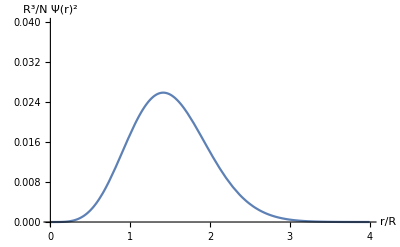

```mathematica
Plot[ΨR[n=1,R=1,l2=2 ,r]^2,{r,0,4},AxesLabel->{"r/R","R^3/N Ψ(r)^2"},PlotRange->{0,0.04}]
```

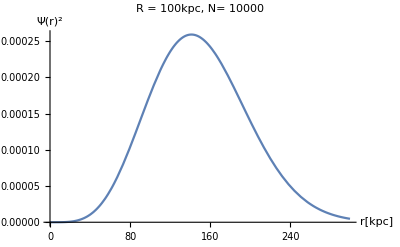

```mathematica
Plot[ΨR[n=10^4,R=100,l2=2 ,r]^2,{r,0,300},AxesLabel->{"r[kpc]","Ψ(r)^2"},PlotRange->Automatic, PlotLabel->"R = 100kpc, N= 10000"]
```

```mathematica
With[{l=2, l2=2},Assuming[{R>0},(4π)^2/(2l+1)(1/r^(l+1)Integrate[rp^(l+2) ΨR[n,R,l2 ,rp]^2,{rp,0,r}]+r^l Integrate[ΨR[n,R,l2 ,rp]^2/rp^(l-1),{rp,r,∞}])]]//Simplify
```

(2 ⅇ^(-r^2/R^2) n √π (-8 r^5-28 r^3 R^2-42 r R^4+21 ⅇ^(r^2/R^2) √π R^5 Erf[r/R]))/(15 r^3 R^3)

```mathematica
f0[n_,R_,r_]:=(4 ⅇ^(-r^2/R^2) n √π (-4 r^3-14 r R^2+15 ⅇ^(r^2/R^2) √π R^3 Erf[r/R]))/(15 r R^3)
```

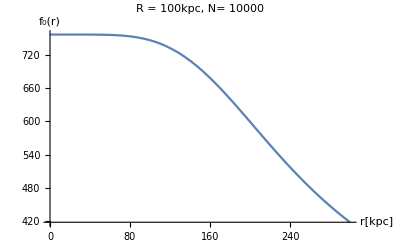

```mathematica
Plot[f0[n=10^4,R=10^2,r],{r,0,300},AxesLabel->{"r[kpc]","f_0(r)"}, PlotLabel->"R = 100kpc, N= 10000"]
```

```mathematica
f2[n_,R_,r_]:=(2 ⅇ^(-r^2/R^2) n √π (-8 r^5-28 r^3 R^2-42 r R^4+21 ⅇ^(r^2/R^2) √π R^5 Erf[r/R]))/(15 r^3 R^3)
```

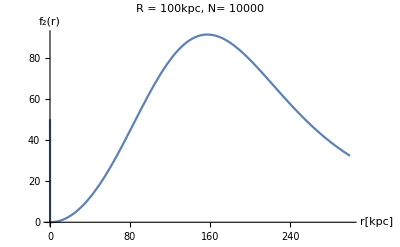

```mathematica
Plot[f2[n=10^4,R=10^2,r],{r,0,300},AxesLabel->{"r[kpc]","f_2(r)"},PlotRange->All, PlotLabel->"R = 100kpc, N= 10000"]
```

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
SphericalHarmonicY[2,0,θ,ϕ]
```

1/4 √(5/π) (-1+3 Cos[θ]^2)

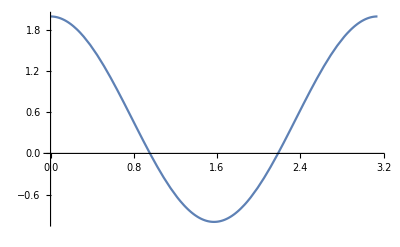

```mathematica
Plot[-1+3 Cos[θ]^2,{θ,0,π}]
```

```mathematica
(1/(2 √π)f0[n,R,r] 1/(2 √π)+√(1/(5π))f2[n,R,r] 1/4 √(5/π) (-1+3 Cos[θ]^2))//Simplify
```

(ⅇ^(-r^2/R^2) n (14 r R^4-2 r (4 r^4+14 r^2 R^2+21 R^4) Cos[θ]^2+ⅇ^(r^2/R^2) √π R^3 (10 r^2-7 R^2+21 R^2 Cos[θ]^2) Erf[r/R]))/(10 √π r^3 R^3)

```mathematica
V[n_,R_,r_,θ_]:=1/(10 √π r^3 R^3)ⅇ^(-r^2/R^2) n (14 r R^4-2 r (4 r^4+14 r^2 R^2+21 R^4) Cos[θ]^2+ⅇ^(r^2/R^2) √π R^3 (10 r^2-7 R^2+21 R^2 Cos[θ]^2) Erf[r/R])
```

```mathematica
-μ^2 V[n,R,r,θ]//Simplify
```

```mathematica
dVdr[r_,θ_]:=(ⅇ^(-r^2/R^2) n μ^2 (8 r^3 R^4+42 r R^6-2 r (8 r^6+20 r^4 R^2+42 r^2 R^4+63 R^6) Cos[θ]^2+ⅇ^(r^2/R^2) √π R^5 (10 r^2-21 R^2+63 R^2 Cos[θ]^2) Erf[r/R]))/(10 √π r^4 R^5)
```

```mathematica
dVdrdθ[r_,θ_]:=(ⅇ^(-r^2/R^2) n μ^2 Cos[θ] (16 r^7+40 r^5 R^2+84 r^3 R^4+126 r R^6-63 ⅇ^(r^2/R^2) √π R^7 Erf[r/R]) Sin[θ])/(5 √π r^4 R^5)
```

```mathematica
dVdθdθ[r_,θ_]:=-(ⅇ^(-r^2/R^2) n μ^2 Cos[2 θ] (8 r^5+28 r^3 R^2+42 r R^4-21 ⅇ^(r^2/R^2) √π R^5 Erf[r/R]))/(5 √π r^3 R^3)
```

```mathematica
dVdrdr[r_,θ_]:=1/(5 √π r^5 R^7)2 ⅇ^(-r^2/R^2) n μ^2 (-2 r R^4 (2 r^4+9 r^2 R^2+21 R^4)+2 r (4 r^8+4 r^6 R^2+16 r^4 R^4+42 r^2 R^6+63 R^8) Cos[θ]^2-ⅇ^(r^2/R^2) √π R^7 (5 r^2-21 R^2+63 R^2 Cos[θ]^2) Erf[r/R])
```

```mathematica
3/ρ dVdr[ρ,π/2]+dVdrdr[ρ,π/2]+1/ρ dVdrdθ[ρ,π/2]//Simplify
```

(n μ^2 (-(2 ⅇ^(-ρ^2/R^2) ρ (21 R^4+24 R^2 ρ^2+8 ρ^4))/(√π R^3)+(21 R^2+10 ρ^2) Erf[ρ/R]))/(10 ρ^5)

```mathematica
-(2 ⅇ^(-ρ^2/R^2) ρ (21 R^4+24 R^2 ρ^2+8 ρ^4))/(√π R^3)+(21 R^2+10 ρ^2) Erf[ρ/R]>0//Simplify
```

```mathematica
(21+10 x^2) Erf[x]>(2 ⅇ^(-x^2) x (21+24  x^2+8 x^4))/(√π)
```

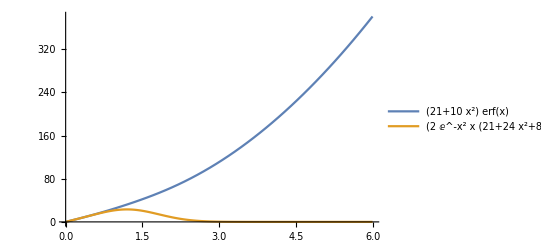

```mathematica
Plot[{(21+10 x^2) Erf[x],(2 ⅇ^(-x^2) x (21+24 x^2+8 x^4))/(√π)},{x,0,6}, PlotLegends->"Expressions"]
```

```mathematica
1/ρ dVdr[ρ,π/2]+1/ρ^2 dVdθdθ[ρ,π/2]+1/ρ dVdrdθ[ρ,π/2]//Simplify
```

(n μ^2 ((2 ⅇ^(-ρ^2/R^2) ρ (63 R^4+32 R^2 ρ^2+8 ρ^4))/(√π R^3)+(-63 R^2+10 ρ^2) Erf[ρ/R]))/(10 ρ^5)

```mathematica
(2 ⅇ^(-ρ^2/R^2) ρ (63 R^4+32 R^2 ρ^2+8 ρ^4))/(√π R^3)+(-63 R^2+10 ρ^2) Erf[ρ/R]>0//Simplify
```

```mathematica
(2 ⅇ^(-x^2) x (63+32 x^2+8 x^4))/(√π)>-(-63 +10 x^2) Erf[x]
```

(2 ⅇ^(-x^2) x (63+32 x^2+8 x^4))/(√π)>(63-10 x^2) Erf[x]

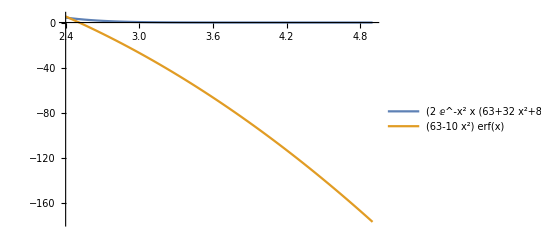

```mathematica
Plot[{(2 ⅇ^(-x^2) x (63+32 x^2+8 x^4))/(√π),(63-10 x^2) Erf[x]},{x,2.4,4.9}, PlotLegends->"Expressions"]
```

```mathematica
ψ[n_,R_,μ_,x_,θ_]:=-1/(10 √π R^3 x^3)ⅇ^(-x^2/(R^2 μ^2)) n (14 R^4 x μ^4-2 x (4 x^4+14 R^2 x^2 μ^2+21 R^4 μ^4) Cos[θ]^2+ⅇ^(x^2/(R^2 μ^2)) √π R^3 μ^3 (10 x^2-7 R^2 μ^2+21 R^2 μ^2 Cos[θ]^2) Erf[x/(R μ)])
```

```mathematica
ψ[n,R,1,r,θ]
```

-(ⅇ^(-r^2/R^2) n (14 r R^4-2 r (4 r^4+14 r^2 R^2+21 R^4) Cos[θ]^2+ⅇ^(r^2/R^2) √π R^3 (10 r^2-7 R^2+21 R^2 Cos[θ]^2) Erf[r/R]))/(10 √π r^3 R^3)

```mathematica
With[{n= 10^4,R=10^2, μ= 1},Plot3D[{ψ[n,R,μ,x,θ]},{x,0,300},{θ,0,π},AxesLabel->{r[kpc],θ,ψ}, PlotLabel->"R = 100kpc, N= 10000"]]
```

-Graphics3D-

```mathematica
With[{R=10^2,n=10^4 ,μ=1},Plot3D[{ψ[n,R,μ,x,θ]},{x,2.5 R,300},{θ,0,π},AxesLabel->{r[kpc],θ,ψ}]]
```

-Graphics3D-

```mathematica
D[ψ[n,R,μ,x,θ],x]//Simplify
```

ψ^(0,0,0,1,0)[n,R,μ,x,θ]

```mathematica
dVdx[n_,R_,μ_,x_,θ_]:= n/(10 √π R^5 x^4 μ^2)(ⅇ^(-x^2/(R^2 μ^2)) (8 R^4 x^3 μ^4+42 R^6 x μ^6-2 x (8 x^6+20 R^2 x^4 μ^2+42 R^4 x^2 μ^4+63 R^6 μ^6) Cos[θ]^2)+ √π R^5 μ^5 (10 x^2-21 R^2 μ^2+63 R^2 μ^2 Cos[θ]^2) Erf[x/(R μ)])
```

```mathematica
dVdx[n_,R_,μ_,x_,θ_]:=n/(10 √π)(ⅇ^(-x^2/(R^2 μ^2))  ((8 R^2 μ^2)/(R^3 x)+(42 R^4 μ^4)/(R^3 x^3)-2/(R^5 x^3 μ^2) (8 x^6+20 R^2 x^4 μ^2+42 R^4 x^2 μ^4+63 R^6 μ^6) Cos[θ]^2)+(√π μ^3)/x^4 (10 x^2-21 R^2 μ^2+63 R^2 μ^2 Cos[θ]^2) Erf[x/(R μ)])
```

```mathematica
D[ψ[n,R,μ,x,θ],θ]/x^2//Simplify
```

-1/(5 √π R^3 x^5)ⅇ^(-x^2/(R^2 μ^2)) n Cos[θ] (8 x^5+28 R^2 x^3 μ^2+42 R^4 x μ^4-21 ⅇ^(x^2/(R^2 μ^2)) √π R^5 μ^5 Erf[x/(R μ)]) Sin[θ]

```mathematica
dVdθ[n_,R_,μ_,x_,θ_]:=-1/(5 √π R^3 x^5) n Cos[θ] (ⅇ^(-x^2/(R^2 μ^2))(8 x^5+28 R^2 x^3 μ^2+42 R^4 x μ^4)-21 √π R^5 μ^5 Erf[x/(R μ)]) Sin[θ]
```

```mathematica
With[{R=10^2,n=10^4 ,μ=1},Plot3D[{-dVdx[n,R,μ,x,θ]},{x,2,300},{θ,0,π}]]
```

-Graphics3D-

```mathematica
With[{R=10^2,n=10^4 ,μ=1},Plot3D[{-dVdθ[n,R,μ,x,θ]},{x,0,300},{θ,0,π}]]
```

-Graphics3D-

```mathematica
With[{R=10^2,n=10^4 ,μ=1},Plot3D[{-Abs[dVdθ[n,R,μ,x,θ]]},{x,0,300},{θ,0,π}]]
```

-Graphics3D-

```mathematica
Clear[n]
```

```mathematica
Spherical Bessel
```

```mathematica
Ψ[n_,k_,r_]:= SphericalBesselJ[n,k r]
```

```mathematica
With[{l=2, l2=2},(4π)^2/(2l+1)(1/r^(l+1)Integrate[rp^(l+2) Ψ[l2,k,rp]^2,{rp,0,r}]+r^l Integrate[Ψ[l2,k,rp]^2/rp^(l-1),{rp,r,∞}])]//Simplify
```

(2 π^2 (-18+9 k^2 r^2+2 k^4 r^4-3 (-6+k^2 r^2) Cos[2 k r]+15 k r Sin[2 k r]))/(3 k^6 r^4)

```mathematica
fb2[k_,r_]:=(2 π^2 (-18+9 k^2 r^2-3 (-6+k^2 r^2) Cos[2 k r]+15 k r Sin[2 k r]))/(3 k^6 r^4)
```

```mathematica
With[{l=0, l2=2},(4π)^2/(2l+1)(1/r^(l+1)Integrate[rp^(l+2) Ψ[l2,k,rp]^2,{rp,0,r}])]//Simplify
With[{l=0, l2=2, rinf=300},Assuming[{Im[r]==0,0<r<rinf},(4π)^2/(2l+1)(r^l Integrate[Ψ[l2,k,rp]^2/rp^(l-1),{rp,r,rinf}])]]//Simplify
```

-(4 π^2 (6+6 k^2 r^2-2 k^4 r^4+6 (-1+k^2 r^2) Cos[2 k r]+k r (-12+k^2 r^2) Sin[2 k r]))/(k^6 r^4)

16 π^2 (-1/(7200000000 k^6)-1/(120000 k^4)+9/(8 k^6 r^4)+3/(4 k^4 r^2)+Cos[600 k]/(7200000000 k^6)-Cos[600 k]/(60000 k^4)-(9 Cos[2 k r])/(8 k^6 r^4)+(3 Cos[2 k r])/(2 k^4 r^2)-CosIntegral[600 k]/(2 k^2)+CosIntegral[2 k r]/(2 k^2)+Log[300]/(2 k^2)+Log[k]/(2 k^2)-Log[k r]/(2 k^2)+Sin[600 k]/(12000000 k^5)-(9 Sin[2 k r])/(4 k^5 r^3))

quitamos los terminos constantes del potencial

```mathematica
fb0[k_,r_]:=(2 π^2 (-3-6 k^2 r^2+4 k^4 r^4+3 Cos[2 k r]+4 k^4 r^4 CosIntegral[2 k r]-4 k^4 r^4 Log[k r]+6 k r Sin[2 k r]-2 k^3 r^3 Sin[2 k r]))/(k^6 r^4)
```

```mathematica
(1/(2 √π)fb0[k,r] 1/(2 √π)+√(1/(5π))fb2[k,r] 1/4 √(5/π) (-1+3 Cos[θ]^2))//Simplify
```

1/(2 k^6 r^4)π (3-9 k^2 r^2+4 k^4 r^4-18 Cos[θ]^2+9 k^2 r^2 Cos[θ]^2+Cos[2 k r] (-3+k^2 r^2-3 (-6+k^2 r^2) Cos[θ]^2)+4 k^4 r^4 CosIntegral[2 k r]-4 k^4 r^4 Log[k r]+k r Sin[2 k r]-2 k^3 r^3 Sin[2 k r]+15 k r Cos[θ]^2 Sin[2 k r])

```mathematica
V[k_,r_,θ_]:=1/(2 k^6 r^4)π (3-9 k^2 r^2+4 k^4 r^4-18 Cos[θ]^2+9 k^2 r^2 Cos[θ]^2+Cos[2 k r] (-3+k^2 r^2-3 (-6+k^2 r^2) Cos[θ]^2)+4 k^4 r^4 CosIntegral[2 k r]-4 k^4 r^4 Log[k r]+k r Sin[2 k r]-2 k^3 r^3 Sin[2 k r]+15 k r Cos[θ]^2 Sin[2 k r])
```

```mathematica
-μ^2 V[μ b,x/μ,θ]//Simplify
```

-1/(2 b^6 x^4)π (3-9 b^2 x^2+4 b^4 x^4-18 Cos[θ]^2+9 b^2 x^2 Cos[θ]^2+Cos[2 b x] (-3+b^2 x^2-3 (-6+b^2 x^2) Cos[θ]^2)+4 b^4 x^4 CosIntegral[2 b x]-4 b^4 x^4 Log[b x]+b x Sin[2 b x]-2 b^3 x^3 Sin[2 b x]+15 b x Cos[θ]^2 Sin[2 b x])

```mathematica
ψadim[b_,x_,θ_]:=-1/(2 b^6 x^4)π (3-9 b^2 x^2+4 b^4 x^4-18 Cos[θ]^2+9 b^2 x^2 Cos[θ]^2+Cos[2 b x] (-3+b^2 x^2-3 (-6+b^2 x^2) Cos[θ]^2)+4 b^4 x^4 CosIntegral[2 b x]-4 b^4 x^4 Log[b x]+b x Sin[2 b x]-2 b^3 x^3 Sin[2 b x]+15 b x Cos[θ]^2 Sin[2 b x])
```

```mathematica
With[{μ=15637.8, b=.000001},Plot3D[ψadim[b,x,θ],{x,0,300 μ},{θ,0,π}]]
```

-Graphics3D-

```mathematica
(*k=(2(Ε μ)/h)^(1/2)*)
```

```mathematica
μ= 15637.8;(*1/kpc*)
```

15.6378

```mathematica
b=10(*((2E)/(μ c^2))^(1/2)*)
```

```mathematica
k= b μhat
```

b μhat

import numpy as np
print(np.pi)

3.141592653589793

```mathematica
D[ψadim[b,x,θ],x]//Simplify
```

1/(2 b^6 x^5)π (12-18 b^2 x^2+4 b^4 x^4-12 Cos[2 b x] (1+3 (-2+b^2 x^2) Cos[θ]^2)-3 b x Sin[2 b x]+Cos[θ]^2 (18 (-4+b^2 x^2)+(81 b x-6 b^3 x^3) Sin[2 b x]))

```mathematica
With[{μ=15637.8, b=.000001},Plot3D[-1/(2 b^6 x^5)π (12-18 b^2 x^2+4 b^4 x^4-12 Cos[2 b x] (1+3 (-2+b^2 x^2) Cos[θ]^2)-3 b x Sin[2 b x]+Cos[θ]^2 (18 (-4+b^2 x^2)+(81 b x-6 b^3 x^3) Sin[2 b x])),{x,2 μ,300 μ},{θ,0,π}]]
```

-Graphics3D-

```mathematica
D[ψadim[b,x,θ],θ]/x^2//Simplify
```

-(3 π (6-3 b^2 x^2+(-6+b^2 x^2) Cos[2 b x]-5 b x Sin[2 b x]) Sin[2 θ])/(2 b^6 x^6)

```mathematica
With[{μ=15637.8, b=.000001},Plot3D[-Abs[(3 π (6-3 b^2 x^2+(-6+b^2 x^2) Cos[2 b x]-5 b x Sin[2 b x]) Sin[2 θ])/(2 b^6 x^6)],{x,2 μ,300 μ},{θ,0,π}]]
```

-Graphics3D-